```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];


vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
maxR = vSg1Data[[Length[vSg1Data]]][[1]];
Print["maxR=",maxR]
maxR = 20;
maxIndex = 40;

Print["R=",vSg1Data[[maxIndex,1]], ", A=",vSg1Data[[maxIndex,4]],", p=", vSg1Data[[maxIndex,5]]];
Print["R=",vSu2Data[[maxIndex,1]], ", A=",vSu2Data[[maxIndex,4]],", p=", vSu2Data[[maxIndex,5]]];
```

maxR=31

R=27, A=5690.91, p=27.1889

R=27, A=210927., p=27.2254

0.00074606

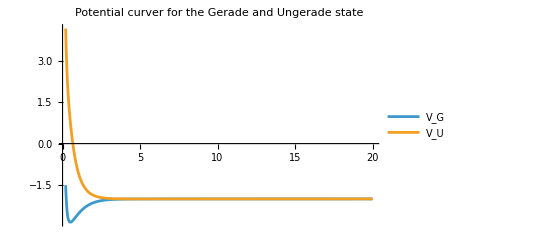

```mathematica
(* Load Potential curves for 1sg, 2sg states 
"R,E, E + 1/R,A,p *)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[vG[r]-vU[r]];
deltaV[20]
Plot[{vG[r],vU[r]},{r,0.2,maxR}, PlotRange->Full, PlotLegends->{"V_G","V_U"}, PlotLabel->"Potential curver for the Gerade and Ungerade state"]
```

```mathematica
(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,a1_,p1_,a2_,p2_, maxDistance_]:=Module[{norm1, norm2,dInt, l1,l2,m1,m2,lmNorm1, lmNorm2},
(* 1s wavefunction *)
l1=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a1 +2 R ξ -p1^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m1=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a1 + p1^2 η^2)M[η]==0, M[0.999]==0,M'[0.999]==1}, M,{η,-.999,.999}];

(* 2s wavefunction *) 
l2=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a2+2 R ξ -p2^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m2=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (-a2 + p2^2 η^2)M[η]==0, M[0.999]==0,M'[0.999]==1}, M,{η,-.999,.999}];

Print["R=",R];
(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=Sqrt[NIntegrate[R^2/4 Abs[l1[ξ]]^2 Abs[ m1[η]]^2 (ξ^2-η^2)/(√(ξ^2-1)√(1-η^2)),{η,-.999,.999},{ξ,1.001,maxDistance}]];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=Sqrt[NIntegrate[R^2/4 Abs[l2[ξ]]^2 Abs[m2[η]]^2(ξ^2-η^2)/(√(ξ^2-1)√(1-η^2)),{η,-.999,.999},{ξ,1.001,maxDistance}]];

dInt=(R/2)^3 1/(norm1 norm2)NIntegrate[l2[ξ]l1[ξ]m1[η]m2[η](ξ η(ξ^2-η^2))/(√(ξ^2-1)√(1-η^2)),{η,-0.999,0.999},{ξ,1.001,maxDistance}];
{R,dInt }
];

singleDR[vSg1Data[[24]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
(*singleDR[vSg1Data[[14]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
singleDR[vSg1Data[[15]][[1]],vSg1Data[[20]][[4]],vSg1Data[[20]][[5]],vSu2Data[[20]][[4]],vSu2Data[[20]][[5]],5]*)
```

R=11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.7776×10^-11 and 6.52924×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.20675×10^-12 and 2.33769×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.86981×10^-15 and 1.79653×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{11,-0.0302729}

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[1;;maxIndex,1]],vSg1Data[[1;;maxIndex,4]],vSg1Data[[1;;maxIndex,5]],vSu2Data[[1;;maxIndex,4]],vSu2Data[[1;;maxIndex,5]]}];

allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], maxR] &, inputData];
```

R=0.2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

R=0.3

R=0.4

R=0.5

R=0.6

R=0.7

R=0.8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.73106×10^-11 and 2.43509×10^-14 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.11234×10^-9 and 1.12412×10^-12 for the integral and error estimates.

R=0.9

R=1.

R=1.1

R=1.5

R=2.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.05577×10^-11 and 1.05557×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

R=2.5

R=3.

R=3.5

R=4.

R=4.5

R=5.

R=6

R=7

R=8

R=9

R=10

R=11

R=12

R=13

R=14

R=15

R=16

R=17

R=18

R=19

R=20

R=21

R=22

R=23

R=24

R=25

R=26

R=27

```mathematica
allDR // MatrixForm
```

(0.2 | 0.0574753
0.3 | -0.44817
0.4 | 0.00883169
0.5 | -0.116574
0.6 | -0.205507
0.7 | -0.259253
0.8 | 0.00101308
0.9 | -0.357497
1. | -0.405411
1.1 | -0.45298
1.5 | 0.625818
2. | 0.00109606
2.5 | 0.129348
3. | 0.176252
3.5 | 0.191681
4. | 0.133112
4.5 | -0.0675202
5. | -4.8693
6 | 0.0144152
7 | 0.654638
8 | 0.0127868
9 | -0.00220667
10 | -0.00243748
11 | 0.00410981
12 | 0.024128
13 | 1.23194
14 | -0.00589267
15 | -0.212951
16 | 0.309602
17 | -0.238177
18 | 0.0127979
19 | 0.130706
20 | 0.0625507
21 | 0.00737499
22 | 1.88059
23 | 0.00596153
24 | -1.26407
25 | -0.180433
26 | -0.231212
27 | 0.0452946)

{{0.2,4.87276×10^-31},{0.3,-3.79958×10^-30},{0.4,7.48751×10^-32},{0.5,-9.88317×10^-31},{0.6,-1.74229×10^-30},{0.7,-2.19794×10^-30},{0.8,8.58893×10^-33},{0.9,-3.03086×10^-30},{1.,-3.43707×10^-30},{1.1,-3.84036×10^-30},{1.5,5.30568×10^-30},{2.,9.29236×10^-33},{2.5,1.09662×10^-30},{3.,1.49427×10^-30},{3.5,1.62507×10^-30},{4.,1.12853×10^-30},{4.5,-5.72436×10^-31},{5.,-4.12819×10^-29},{6,1.22212×10^-31},{7,5.55002×10^-30},{8,1.08406×10^-31},{9,-1.87082×10^-32},{10,-2.0665×10^-32},{11,3.4843×10^-32},{12,2.04557×10^-31},{13,1.04444×10^-29},{14,-4.99581×10^-32},{15,-1.8054×10^-30},{16,2.6248×10^-30},{17,-2.01927×10^-30},{18,1.08501×10^-31},{19,1.10812×10^-30},{20,5.30304×10^-31},{21,6.25251×10^-32},{22,1.59437×10^-29},{23,5.05419×10^-32},{24,-1.07168×10^-29},{25,-1.52971×10^-30},{26,-1.96022×10^-30},{27,3.84007×10^-31}}

InterpolatingFunction::dmval: Input value {0.100141} lies outside the range of data in the interpolating function. Extrapolation will be used.

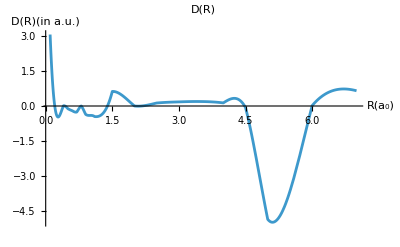

InterpolatingFunction::dmval: Input value {0.100407} lies outside the range of data in the interpolating function. Extrapolation will be used.

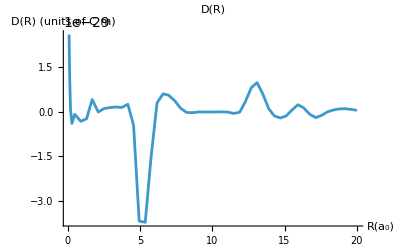

```mathematica
(* Dipole moment in SI units *)
drAUtoSI = 8.478*^-30; (* Cm *)
allDRSI=allDR;
allDRSI[[All,2]] =allDR[[All,2]]*drAUtoSI;
allDRSI

dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
Plot[dR[r],{r,0.1, 7}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R)(in a.u.)"}, PlotRange->Full]

dRSI =Interpolation[Transpose[{allDRSI[[All,1]],allDRSI[[All,2]]}], InterpolationOrder->3];
Plot[dRSI[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R) (units of C m)"}, PlotRange->Full, Axes->True]
```

```mathematica
aR[R_]:=4/(3hbar cLight^3)(dR[R])^2((vU[R]-vG[R])/hbar)^3;
aR[1]
```

3.07295×10^-7

1.41339

1.41339

InterpolatingFunction::dmval: Input value {0.100018} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

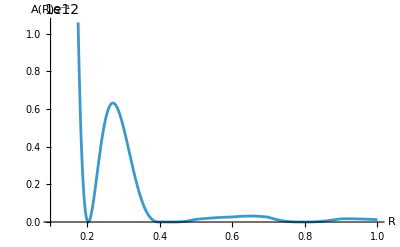

InterpolatingFunction::dmval: Input value {0.100018} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

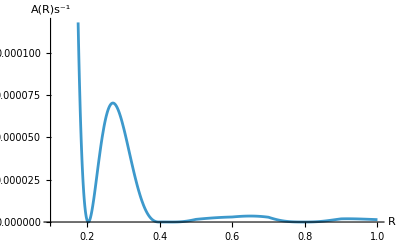

```mathematica
aRAUtoSI = 4.1341*^16;
aRSI[R_]:=aR[R]*aRAUtoSI;
aRSI2[1]
aRSI2[R_]:=4/(3 hbarSI cLightSI^3)(dRSI[R])^2(((vU[R]-vG[R])4.35974*^-18)/hbarSI)^3;
aRSI2[1]

Plot[aRSI[R],{R,0.1,1},AxesLabel->{"R", "A(R)s^-1"}]

Plot[aRSI2[R]*10^-6,{R,0.1,1},AxesLabel->{"R", "A(R)s^-1"}]
```